```mathematica
2-2
```

0

```mathematica
Adiabatic Invariance Theorem
```

Nicholas Wheeler
Reed College Physics Department
2 December 2008

Here are a pair of oscillator Hamiltonians:

```mathematica
Subscript[H, 0]=1/2 p^2+1/2 Subscript[ω, 0]^2 x^2
Subscript[H, 1]=1/2 p^2+1/2 Subscript[ω, 1]^2 x^2
```

We will suppose that the characteristic angular frequencies are

```mathematica
Subscript[ω, 0]=1
Subscript[ω, 1]=2
```

The associated periods are

```mathematica
Subscript[τ, 0]=2π
Subscript[τ, 1]=π
```

Here are isoenergetic curves (energies 1, 2, 3, 4, 5) of H_0 and H_1:

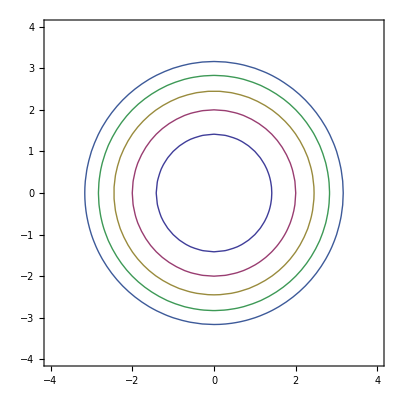

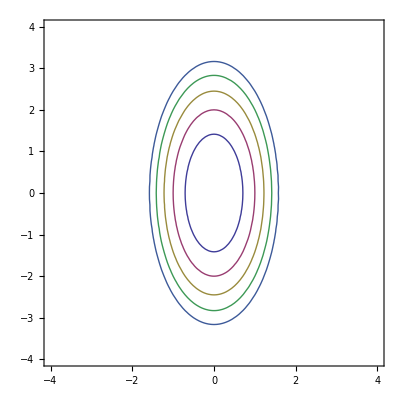

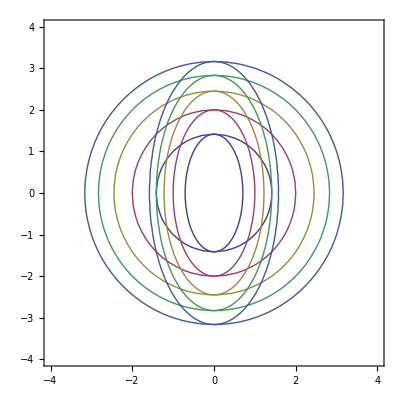

Here (at time t = 0) are phase points ("particles") that have been chasing each other around the E = 1 curve of H_0:

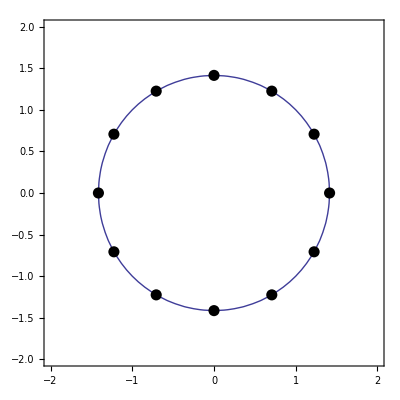

-Graphics3D-

### Abrupt transition: H_0→H_1

An external agent abruptly adjusts the parameter ω_0→ω_1, with this consequence:

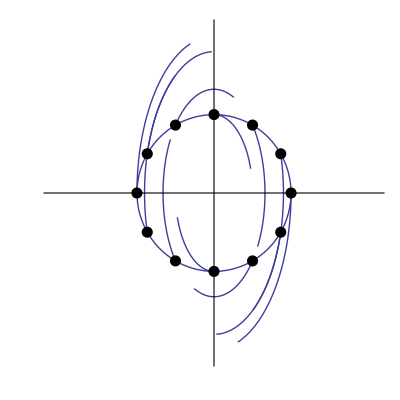

Note that the particles possess now assorted energies, depending upon their placement at the moment of transition:

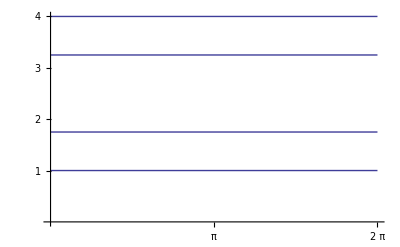

### Brisk but continuous transition

Introduce the interpolating Hamiltonian

```mathematica
H[t]=1/2 p^2+1/2 ω[t]^2 x^2
```

where ω[t] has (say) the form

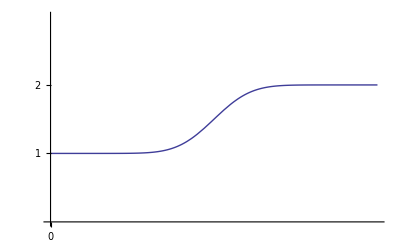

and rises from ω_0=1 to ω_1=2 in a characteristic time T that is under our control. We set

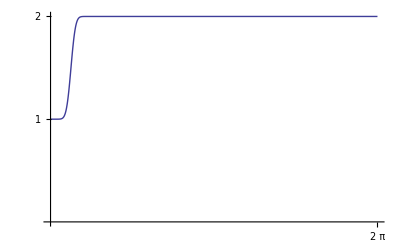

```mathematica
T=Subscript[τ, 0]/8=π/4
```

The phase trajectories of the particles (show below for the noon, 1, 2 and 3 o'clock particles) are rapidly but continuously diverted

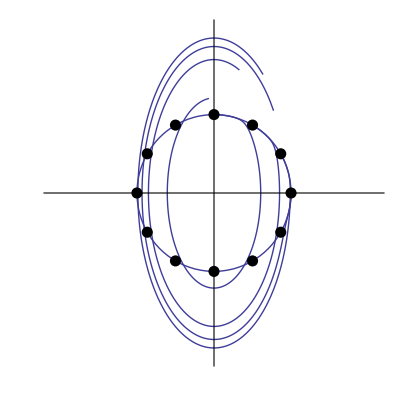

and they acquire assorted energies:

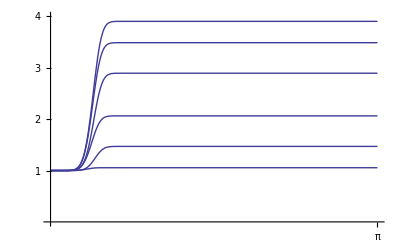

Here again, the asymptotic energies are sensitive to initial conditions (initial placement on the circle). They are more numerous than they were when the transition was instantaneous, and the difference Energy_greatest-Energy_least is a little bit smaller than it was before.

### Less brisk transition

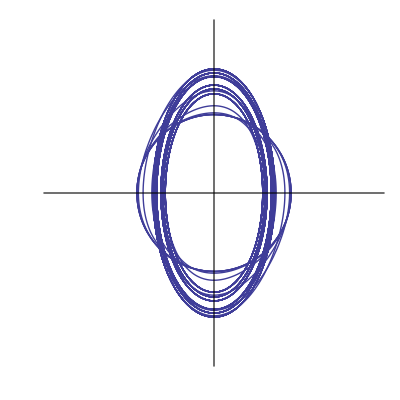

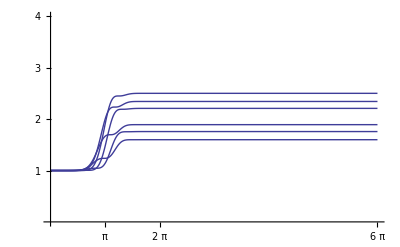

```mathematica
T=Subscript[τ, 0]=2π
```

Slowing down the transition has caused the asymptotic energies to be more tightly grouped.

### Slow transition

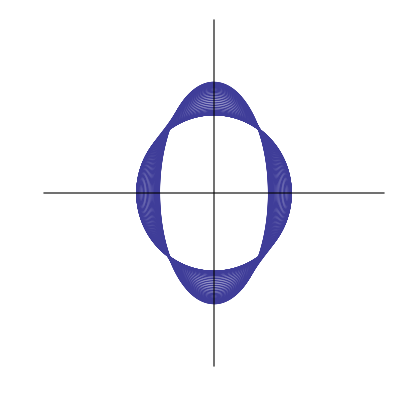

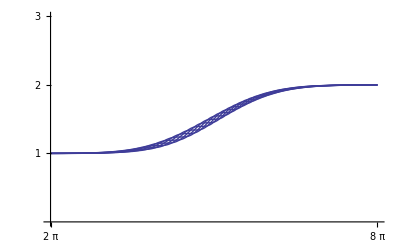

```mathematica
T=5 Subscript[τ, 0]=10π
```

The post-transitional energies are now nearly the same. Consequences of the fact that they initially occupied distinct places on the isoenergetic circle have been nearly washed out.

### Very slow transition

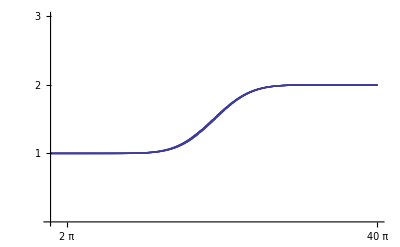

```mathematica
T=20 Subscript[τ, 0]=40π
```

The particles, which started out with identical energies, now maintain nearly identical energies throughout the transition.

Initially they chased each other around the following isoenergetic curve of H_0:

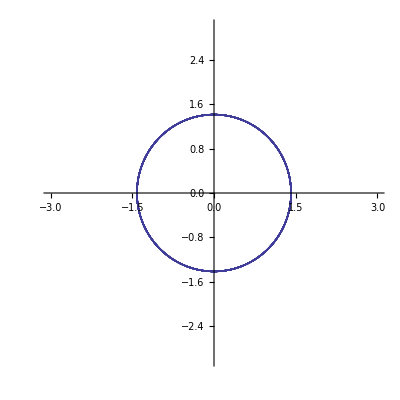

Ultimately they chase each other around the following isoenergetic curve of H_1:

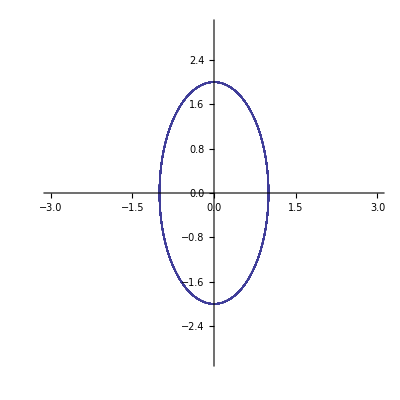

Notice that the ellipses have the same area:

Area_0=Area_1

To say the same thing another way,

J_0=J_1

which is the upshot of the adiabatic invariance theorem. To say the same thing in yet another way,

E_0/ω_0=E_1/ω_1
E_1=(ω_1/ω_0)E_0

E_1-E_0= work done by agent that executed the transition

### Parametric cycles

Suppose ω[t] has the form shown below:

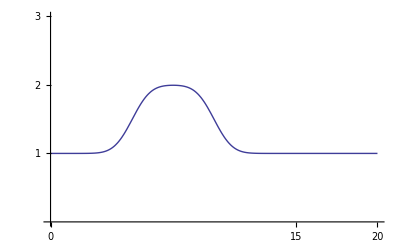

I will call such parametric excursions "cycles" because, though when ω-space is one-dimensional they are simple "to-and-fro" exercises, when ω-space is multidimensional the excursion traces a closed path or "cycle" in parameter space.

If the cycle is abrupt the initially isoenergic motion of the particles will become permanently disrupted—for reasons, and in a way, that we are in position now to understand. 

If, on the other hand, the cycle is pursued very slowly, J will clearly remain constant throughout the process, and the particles will end up back on their initial circular isoenergetic curve. The interesting question is: WHERE—COMPARED TO WHERE THEY OTHERWISE WOULD HAVE BEEN—WILL THEY BE ON THAT CIRCULAR CURVE?

By numerically integrating the equations of motion of the particle that stood initially at 3 o'clock, and that moved
   • undisturbed by any parametric variation
   • subject to a "fact cycle" that was complete by time T=60 τ_0
   • subject to a "slow cycle" that was complete by time T=120 τ_0
I obtained functions

UndisturbedX[t]
UndisturbedP[t]
FastCycleX[t]
FastCycleP[t]
SlowCycleX[t]
SlowCycleP[t]

from which I constructed comparison functions

FastΔX[t]:=FastCycleX[t]-UndisturbedX[t]
FastΔP[t]:=FastCycleP[t]-UndisturbedP[t]
SlowΔX[t]:=SlowCycleX[t]-UndisturbedX[t]
SlowΔP[t]:=SlowCycleP[t]-UndisturbedP[t]

I then constructed a table showing

n      FastΔX[t]     SlowΔX[t]

at times

t→58π+2 π/10 n       :      {n,0,10}
t→118π+2 π/10 n     :      {n,0,10}

respectively, with this result:

0 | -0.00310239 | -0.00155082
1 | -0.00251108 | -0.00125418
2 | -0.000960672 | -0.000478639
3 | 0.000956495 | 0.000479695
4 | 0.00250833 | 0.0012549
5 | 0.003102 | 0.00155071
6 | 0.00251095 | 0.00125396
7 | 0.000960724 | 0.000478657
8 | -0.000956643 | -0.000479849
9 | -0.00250819 | -0.00125487
10 | -0.00310192 | -0.00155065

Ditto for

n      FastΔP[t]     SlowΔP[t]

with this result

0 | -1.65715×10^-6 | 8.36972×10^-7
1 | 0.00182183 | 0.000912153
2 | 0.00294974 | 0.00147505
3 | 0.00295094 | 0.00147466
4 | 0.00182504 | 0.000910985
5 | 2.03846×10^-6 | -8.97003×10^-7
6 | -0.00182139 | -0.000912278
7 | -0.00294945 | -0.00147496
8 | -0.00295074 | -0.00147455
9 | -0.00182508 | -0.000910933
10 | -2.01856×10^-6 | 6.55535×10^-7

We see that the 3 o'clock particle is at those time at nearly the same position of the circle, whether its motion was undisturbed or subject to a fast cycle, and that the agreement was even better if the was slow (meaning here that it took twice as long). 

The implication appears to be that completion of an adiabatic cycle leaves θ unchanged from what it would have been in the absence of parametric adjustment. This is a remarkable result, and made the more remarkable by Hannay's theorem (Jose & Saletan, §6.4.3 (pages 365–371)).